## Example 13.2

```mathematica
Remove["Global`*"]
```

```mathematica
f=y*(x+1);
g=x*(y+1);
```

```mathematica
(* Find the fixed points *)
```

```mathematica
fps=Solve[{f==0,g==0},{x,y}]
```

{{x→-1,y→-1},{x→0,y→0}}

```mathematica
(* Compute the Jacobian matrix *)
```

```mathematica
A={{D[f,x],D[f,y]},{D[g,x],D[g,y]}};
```

```mathematica
(* We will label the origin as fps1 *)
```

```mathematica
Afps1=A/.fps[[2]];
Afps2=A/.fps[[1]];
```

```mathematica
Print["The eigenvalues of the origin are ", Eigenvalues[Afps1]]
```

The eigenvalues of the origin are {-1,1}

```mathematica
Print["The eigenvalues of (-1,-1) are ", Eigenvalues[Afps2]]
```

The eigenvalues of (-1,-1) are {-1,-1}

```mathematica
Print["The eigenvectors of the origin are ", Eigenvectors[Afps1]]
```

The eigenvectors of the origin are {{-1,1},{1,1}}

```mathematica
Print["The eigenvectors of (-1,-1) are ", Eigenvectors[Afps2]]
```

The eigenvectors of (-1,-1) are {{0,1},{1,0}}

## Example 13.3

```mathematica
Remove["Global`*"]
```

```mathematica
tmax=6; 

soln1=NDSolve[{x'[t]==y[t](x[t]+1),y'[t]==x[t](y[t]+1),x[0]==-0.001,y[0]==0.001},{x,y},{t,0,-tmax}];
soln2=NDSolve[{x'[t]==y[t](x[t]+1),y'[t]==x[t](y[t]+1),x[0]==0.001,y[0]==-0.001},{x,y},{t,0,-tmax}];
soln3=NDSolve[{x'[t]==y[t](x[t]+1),y'[t]==x[t](y[t]+1),x[0]==0.001,y[0]==0.0011},{x,y},{t,0,tmax}];
soln4=NDSolve[{x'[t]==y[t](x[t]+1),y'[t]==x[t](y[t]+1),x[0]==-0.001,y[0]==-0.001},{x,y},{t,0,tmax}];
```

```mathematica
stable1=ParametricPlot[{x[t],y[t]}/.soln1,{t,0,-tmax},PlotStyle->Black];
stable2=ParametricPlot[{x[t],y[t]}/.soln2,{t,0,-tmax},PlotStyle->Black];
unstable1=ParametricPlot[{x[t],y[t]}/.soln3,{t,0,tmax},PlotStyle->Black];
unstable2=ParametricPlot[{x[t],y[t]}/.soln4,{t,0,tmax},PlotStyle->Black];
```

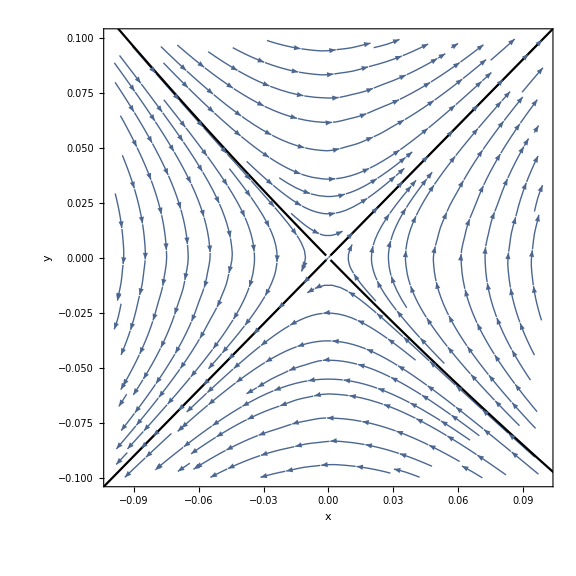

```mathematica
stream=StreamPlot[{y(x+1),x(y+1)},{x,-0.1,0.1},{y,-0.1,0.1},StreamColorFunction->Blue];

Show[stream,stable1,stable2,unstable1,unstable2,Frame->True,Axes->False,BaseStyle->{Bold,FontSize->16},FrameLabel->{"x","y"}]
```

## Example 13.5

```mathematica
Remove["Global`*"]
```

```mathematica
soln1=NDSolve[{x'[t]==y[t],y'[t]==x[t](1-x[t]^2)-0.1*y[t],x[0]==0.01,y[0]==0},{x,y},{t,0,100}];
unstable1=ParametricPlot[Evaluate[{x[t],y[t]}/.soln1],{t,0,100},PlotStyle->Black,PlotRange->{{-2.1,2.1},{-2.1,2.1}}];

soln2=NDSolve[{x'[t]==y[t],y'[t]==x[t](1-x[t]^2)-0.1*y[t],x[0]==0.01,y[0]==0},{x,y},{t,0,-40}];
stable1=ParametricPlot[Evaluate[{x[t],y[t]}/.soln2],{t,0,-20},PlotStyle->Red,PlotRange->{{-2.1,2.1},{-2.1,2.1}}];

soln3=NDSolve[{x'[t]==y[t],y'[t]==x[t](1-x[t]^2)-0.1*y[t],x[0]==-0.01,y[0]==0},{x,y},{t,0,100}];
unstable2=ParametricPlot[Evaluate[{x[t],y[t]}/.soln3],{t,0,100},PlotStyle->Black,PlotRange->{{-2.1,2.1},{-2.1,2.1}}];

soln4=NDSolve[{x'[t]==y[t],y'[t]==x[t](1-x[t]^2)-0.1*y[t],x[0]==-0.01,y[0]==0},{x,y},{t,0,-40}];
stable2=ParametricPlot[Evaluate[{x[t],y[t]}/.soln4],{t,0,-20},PlotStyle->Red,PlotRange->{{-2.1,2.1},{-2.1,2.1}}];
```

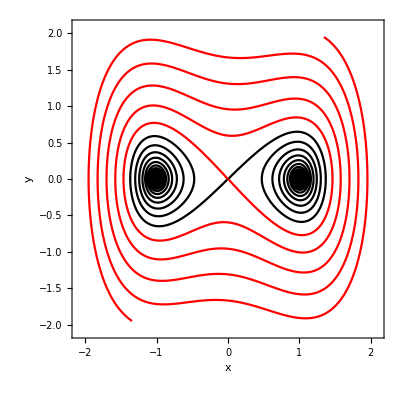

```mathematica
Show[unstable1,unstable2,stable1,stable2,FrameLabel->{"x","y"},BaseStyle->{FontSize->16},Frame->True,Axes->False]
```

## Example 13.6

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[{Plot,ListPlot,ParametricPlot},Axes->False,Frame->True,BaseStyle->{FontSize->16},ImageSize->Large];
```

```mathematica
soln=NDSolve[{x''[t]+0.15*x'[t]-x[t]+x[t]^3==0.3*Cos[t],x[0]==0,x'[0]==0},x,{t,0,5000}];
```

```mathematica
p1=Plot[x[t]/.soln,{t,4500,5000},FrameLabel->{"time","x(t)"},PlotLabel->"x(t)"];
```

```mathematica
p2=ParametricPlot[{x[t],x'[t]}/.soln,{t,4500,5000},FrameLabel->{"x","v"},PlotLabel->"Phase Portrait"];
```

```mathematica
psData=Table[{First[x[t]/.soln],First[x'[t]/.soln]},{t,1000,5000,2*π}];
```

```mathematica
p3=ListPlot[psData,FrameLabel->{"x","v"},PlotLabel->"Poincare Section"];
```

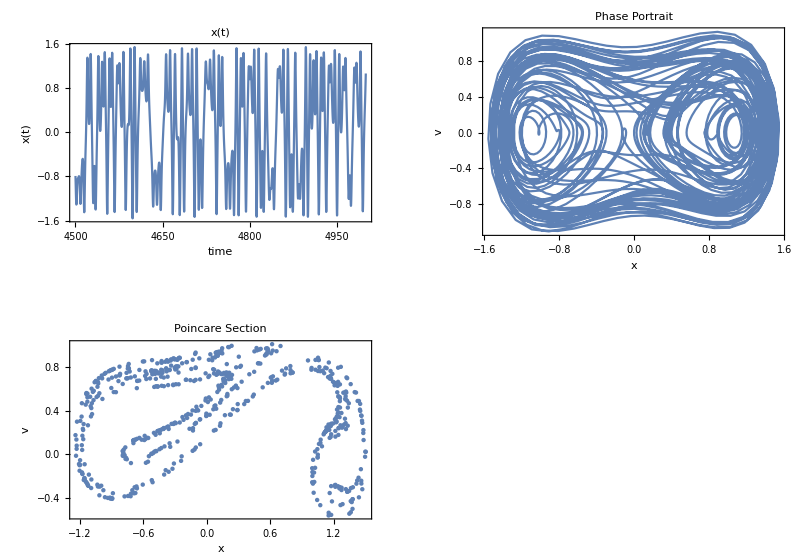

```mathematica
GraphicsGrid[{{p1,p2},{p3}}]
```